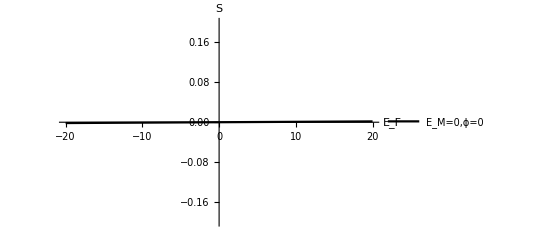

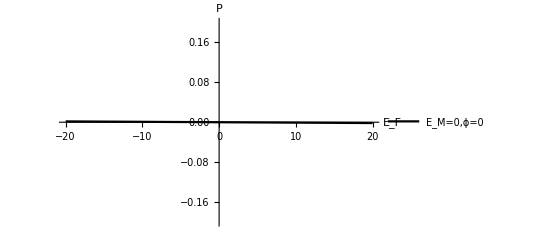

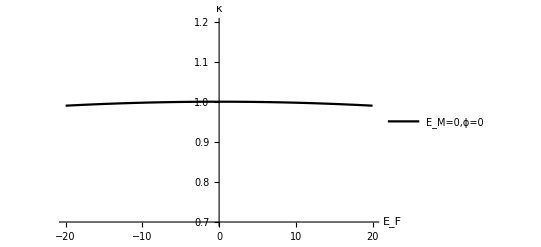

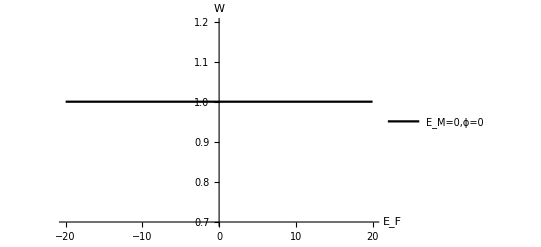

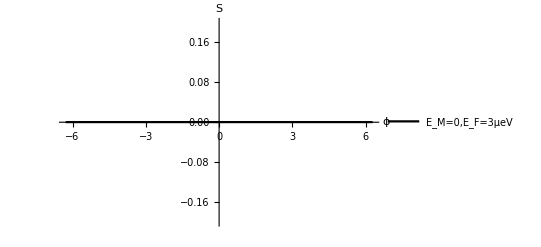

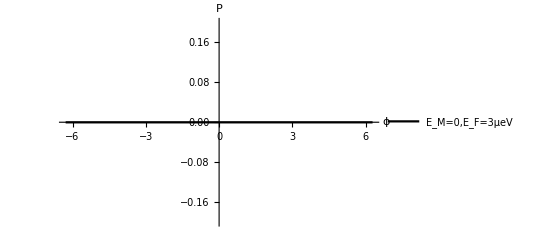

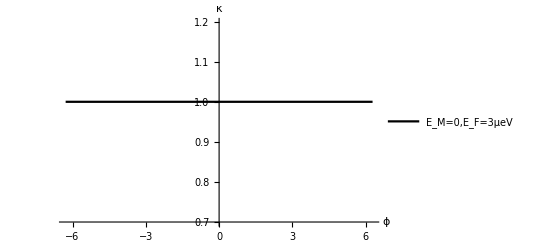

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in E0 near {E0} = {3.197}. NIntegrate obtained 7.63278×10^-17 and 1.5675×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in E0 near {E0} = {3.197}. NIntegrate obtained 7.63278×10^-17 and 1.5675×10^-16 for the integral and error estimates.

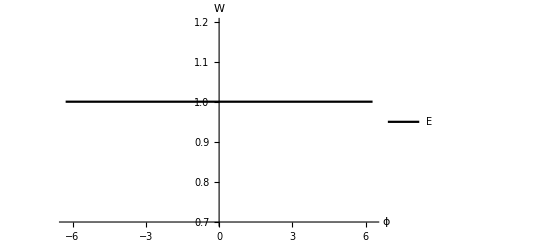

```mathematica
kbT = 1;                (*T = 115mK, E0 and Ef are in units of μeV*)
df[E0_,Ef_] := (ⅇ^((E0-Ef)/kbT)/((1+ⅇ^((E0-Ef)/kbT))^2 kbT));
(*Partial derivative of Fermi function with respect to incident electron energy*)









(*Defining the transmission probability*)

T1[E0_,Ef_,V_,phi_,Em_] := Abs[1/2 ⅇ^((ⅈ E0)/200+(ⅈ Ef)/200-(ⅈ phi)/2) (1+ⅇ^((ⅈ E0)/200+(ⅈ Ef)/200))]^2





(*Different values of Em in μeV*)
Emaj = 10;



(*Different elements of the Onsager matrix, change last input of transmission probability to change Em*)
LeTt[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ] :=( ((E0 - (Ef))/kbT)^(1)) (T1[(E0),Ef,0,phi,Em])(df[E0/kbT,Ef/kbT])
LeVv[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ] :=( ((E0 - (Ef))/kbT)^(0)) (T1[(E0),Ef,0,phi,Em])(df[E0/kbT,Ef/kbT])
LhVv[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ] :=( ((E0 - (Ef))/kbT)^(1)) (T1[(E0),Ef,0,phi,Em])(df[E0/kbT,Ef/kbT])
LhTt[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ] :=( ((E0 - (Ef))/kbT)^(2)) (T1[(E0),Ef,0,phi,Em])(df[E0/kbT,Ef/kbT])

LeV[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ] := NIntegrate[ LeVv[(E0), fer,Em,phi], {E0, -Infinity, Infinity}]

LeT[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ] := NIntegrate[LeTt[(E0), fer, Em,phi]    , {E0, -Infinity, Infinity}]

LhV[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ] := NIntegrate[LhVv[(E0), fer, Em,phi]        , {E0, -Infinity, Infinity}]

LhT[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ] := NIntegrate[LhTt[(E0), fer, Em,phi]  , {E0, -Infinity, Infinity}]


(*Thermoelectric parameters acquired from the Onsager matrix elements*)
k[fer_, Em_, phi_] :=(1/(2))((LeT[fer, Em, phi])^2/(2*(LeV[fer, Em, phi]*LhT[fer, Em, phi])-(LeT[fer, Em, phi]*LhV[fer, Em, phi])))
p[fer_, Em_, phi_] := (1/(4*1)) * ((LeT[fer, Em, phi])^2)/LeV[fer, Em, phi]
S[fer_, Em_, phi_] := -LeT[fer, Em, phi]/LeV[fer, Em, phi]
kappa[fer_, Em_, phi_] := ((LeV[fer, Em, phi]*LhT[fer, Em, phi] - LhV[fer, Em, phi]*LeT[fer, Em, phi])/ (LeV[fer, Em, phi]))/3.285
P[fer_, Em_, phi_] := (LhV[fer, Em, phi]/LeV[fer, Em, phi])(1)
z0[fer_, Em_, phi_] := Em*11.5*(LeV[fer, Em, phi](S[fer, Em, phi])^2/(kappa[fer, Em, phi]))/(1)
Nmax[fer_, Em_, phi_]:=(Sqrt[z0 [fer, Em, phi] + 1] - 1)/(Sqrt[z0[fer, Em, phi] + 1] + 1)
Pmaxr[fer_, Em_, phi_]:= Sqrt[(LhT[fer, Em, phi])(LeV[fer, Em, phi]*LhT[fer, Em, phi] - LhV[fer, Em, phi]*LeT[fer, Em, phi])/(LeV[fer, Em, phi])]







(*Plotting the functions*)
Plot[{S[fer, 0, 0]}, {fer, -20,20}, AxesLabel->{Text[Style["E_F", FontSize->20]], Text[Style["S", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick},{Yellow, Dashed, Thick}, {Darker[Darker[Green]], Dashed, Thick}}, PlotLegends->{"E_M=0,ϕ=0", "E_M≠0,ϕ=0", "E_M=0,ϕ=π/6", "E_M≠0, ϕ=π/6"},PlotPoints->10,PlotRange->{-0.2,0.2}]
Plot[{P[fer, 0,0]}, {fer, -20,20}, AxesLabel->{Text[Style["E_F", FontSize->20]], Text[Style["P", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick},{Yellow, Dashed, Thick}, {Darker[Darker[Green]], Dashed, Thick}}, PlotLegends->{"E_M=0,ϕ=0", "E_M≠0,ϕ=0", "E_M=0,ϕ=π/6", "E_M≠0, ϕ=π/6"}, PlotPoints->10,PlotRange->{-0.2,0.2}]
Plot[{kappa[fer, 0,0]}, {fer, -20,20}, AxesLabel->{Text[Style["E_F", FontSize->20]], Text[Style["κ", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick},{Yellow, Dashed, Thick}, {Darker[Darker[Green]], Dashed, Thick}}, PlotLegends->{"E_M=0,ϕ=0", "E_M≠0,ϕ=0", "E_M=0,ϕ=π/6", "E_M≠0, ϕ=π/6"}, PlotPoints->10, PlotRange->{0.7,1.2}]

Plot[{kappa[fer, 0, 0]/LeV[fer,0, 0]}, {fer, -20,20}, AxesLabel->{Text[Style["E_F", FontSize->20]], Text[Style["W", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick},{Yellow, Dashed, Thick}, {Darker[Darker[Green]], Dashed, Thick}}, PlotLegends->{"E_M=0,ϕ=0", "E_M≠0,ϕ=0", "E_M=0,ϕ=π/6", "E_M≠0, ϕ=π/6"}, PlotPoints->10, PlotRange->{0.7,1.2}]




Plot[{S[3, 0, phi]}, {phi, -2*Pi,2*Pi}, AxesLabel->{Text[Style["ϕ", FontSize->20]], Text[Style["S", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick}}, PlotLegends->{"E_M=0,E_F=3μeV", "E_M≠0,E_F=3μeV"},PlotPoints->10,PlotRange->{-0.2,0.2}]
Plot[{P[3, 0,phi]}, {phi, -2*Pi,2*Pi}, AxesLabel->{Text[Style["ϕ", FontSize->20]], Text[Style["P", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick}}, PlotLegends->{"E_M=0,E_F=3μeV", "E_M≠0,E_F=3μeV"}, PlotPoints->10,PlotRange->{-0.2,0.2}]
Plot[{kappa[3, 0,phi]}, {phi, -2*Pi,2*Pi}, AxesLabel->{Text[Style["ϕ", FontSize->20]], Text[Style["κ", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick}}, PlotLegends->{"E_M=0,E_F=3μeV", "E_M≠0,E_F=3μeV"}, PlotPoints->10, PlotRange->{0.7,1.2}]

Plot[{kappa[0, 0, phi]/LeV[0,0, phi]}, {phi, -2*Pi,2*Pi}, AxesLabel->{Text[Style["ϕ", FontSize->20]], Text[Style["W", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick},{Yellow, Thick}, {Darker[Darker[Green]], Dashed, Thick}}, PlotLegends->{"E", "E_M≠0,E_F=0", "E_M=0,E_F=10μeV", "E_M≠0, E_F=10μeV"}, PlotPoints->10, PlotRange->{0.7,1.2}]


(*
Plot[{p[phi, 0], p[phi,Emaj], p[phi,Emaj1], p[phi,Emaj2]}, { phi, -20,20}, AxesLabel->{Text[Style["Ef(meV)", FontSize->20]], Text[Style["P_Max", FontSize->20]]},PlotStyle->{{Black, Thick},{Red, Dashed, Thick}, {Orange, Dashed, Thick}, {Yellow,Dashed,Thick}}, PlotPoints->10, PlotRange->All]
Plot[{k[phi, 0], k[phi,Emaj], k[phi,Emaj1], k[phi,Emaj2]},  {phi, -20,20}, AxesLabel->{Text[Style["Ef(meV)", FontSize->20]], Text[Style["η_maxP", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick}, {Orange, Dashed, Thick}, {Yellow,Dashed,Thick}}, PlotPoints->10, PlotRange->All]
Plot[{z0[phi, 0], z0[phi,Emaj], z0[phi,Emaj1], z0[phi,Emaj2]},  {phi, -20,20}, AxesLabel->{Text[Style["Ef(meV)", FontSize->20]], Text[Style["Z_T", FontSize->20]]},PlotStyle->{{Black, Thick},{Red, Dashed, Thick}, {Orange, Dashed, Thick}, {Yellow,Dashed,Thick}}, PlotPoints->10, PlotRange->All]
Plot[{3.26*LeV[phi, 0]/kappa[phi,0], 3.26*LeV[phi,Emaj]/kappa[phi,Emaj],3.26*LeV[phi,Emaj1]/kappa[phi,Emaj1],3.26*LeV[phi,Emaj2]/kappa[phi,Emaj2]}, {phi, -60,60}, AxesLabel->{Text[Style["Ef(meV)", FontSize->20]], Text[Style["L", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick}, {Orange, Dashed, Thick}, {Yellow,Dashed,Thick}},PlotPoints->10, PlotRange->All]
Plot[{Pmaxr[phi, 0], Pmaxr[phi,Emaj],Pmaxr[phi,Emaj1],Pmaxr[phi,Emaj2]},  {phi, -20,20}, AxesLabel->{Text[Style["Ef(meV)", FontSize->20]], Text[Style["P^r", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick}, {Orange, Dashed, Thick}, {Yellow,Dashed,Thick}}, PlotPoints->10, PlotRange->All]
Plot[{kappa[phi, 0], kappa[phi,Emaj],kappa[phi,Emaj1],kappa[phi,Emaj2]}, {phi, -20,20}, AxesLabel->{Text[Style["Ef(meV)", FontSize->20]], Text[Style["κ", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick}, {Orange, Dashed, Thick}, {Yellow,Dashed,Thick}}, PlotPoints->10, PlotRange->All]
Plot[{Nmax[phi, 0], Nmax[phi,Emaj], Nmax[phi,Emaj1], Nmax[phi,Emaj2]},  {phi, -20,20}, AxesLabel->{Text[Style["Ef(meV)", FontSize->20]], Text[Style["P^r", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick}, {Orange, Dashed, Thick}, {Yellow,Dashed,Thick}}, PlotPoints->10, PlotRange->All]
*)
```